## A1. LELBC: caratteristica differenziale e recupero parziale di chiave

### S-Box

```mathematica
(*indici hex: 0 1 2 3 4 5 6 7 8 9 A B C D E F*)
SBox={12,14,6,10,4,15,2,7,9,8,3,11,0,13,1,5}
```

{12,14,6,10,4,15,2,7,9,8,3,11,0,13,1,5}

### Key schedule

```mathematica
LELBCKeySchedule[masterKey128_Integer,numRounds_Integer:16]:=Module[{keyState,subkeys={},k124to127,k121to124,kLeft,kRight,i},
(*la chiave è un vettore di 128 bit
keyState[[1]] corrisponde a k0, keyState[[128]] corrisponde a k127*)
keyState=IntegerDigits[masterKey128,2,128];
For[i=1,i<=numRounds,i++,
(*SBOX SU k124||k125||k126||k127*)
k124to127=FromDigits[keyState[[125;;128]],2];
keyState[[125;;128]]=IntegerDigits[SBox[[k124to127+1]],2,4];

(*XOR i CON k121||k122||k123||k124*)
k121to124=FromDigits[keyState[[122;;125]],2];
keyState[[122;;125]]=IntegerDigits[BitXor[k121to124,i-1],2,4];

(*ROTAZIONE DELLA CHIAVE DI 64 BIT*)
keyState=Join[keyState[[65;;128]],keyState[[1;;64]]];

(*ROTAZIONE SINISTRA DI 9 BIT DELLA PRIMA META'*)
kLeft=Join[keyState[[10;;64]],keyState[[1;;9]]];

(*ROTAZIONE SINISTRA DI 15 BIT DELLA SECONDA META'*)
kRight=Join[keyState[[80;;128]],keyState[[65;;79]]];
keyState=Join[kLeft,kRight];

(*ESTRAZIONE DELLA ROUND KEY*)
AppendTo[subkeys,{FromDigits[keyState[[1;;32]],2],FromDigits[keyState[[33;;64]],2]}];];
subkeys
];
```

### Sublayer

```mathematica
(*applica l'sbox a un intero da 32 bit decimale *)
ApplySubLayer[x_Integer]:=FromDigits[SBox[[#+1]]&/@IntegerDigits[x,16,8],16];
```

### Left circular shift

```mathematica
LeftRotate5[x_Integer]:=BitOr[BitAnd[BitShiftLeft[x,5],16^^FFFFFFFF],BitShiftRight[x,27]];
```

### Round function

```mathematica
LELBCRound[{X0_,X1_},{K0_,K1_}]:=Module[{A0,A1},
A0=BitXor[X0,K0];
A1=BitXor[X1,LeftRotate5[A0]];
A0=ApplySubLayer[A0];
A1=ApplySubLayer[A1];
A0=BitXor[A0,LeftRotate5[A1]];
A1=BitXor[A1,K1];
{A0,A1}];
```

### Encrypt

```mathematica
LELBCEncrypt[{P0_,P1_},subkeys_List]:=Module[{state},
state=Fold[LELBCRound,{P0,P1},subkeys];
(*permutazione finale algoritmo 2*)
Reverse[state]];
```

### Round inverso

```mathematica
LELBCInverseRound[{X0_,X1_},{K0_,K1_}]:=Module[{A0=X0,A1=X1},A1=BitXor[A1,K1];
A0=BitXor[A0,LeftRotate5[A1]];
A0=ApplySubLayer[A0];
A1=ApplySubLayer[A1];
A1=BitXor[A1,LeftRotate5[A0]];
A0=BitXor[A0,K0];
{A0,A1}];
```

### Decrypt

```mathematica
LELBCDecrypt[ciphertext_List,subkeys_List]:=Fold[LELBCInverseRound,Reverse[ciphertext],Reverse[subkeys]];
```

#### TEST ENCRYPT/DECRYPT

```mathematica
testMasterKey=16^^0123456789ABCDEFFEDCBA9876543210;
testPlaintext={16^^01234567,16^^89ABCDEF};
testKeys=LELBCKeySchedule[testMasterKey,16];
testCiphertext=LELBCEncrypt[testPlaintext,testKeys];
testDecrypted=LELBCDecrypt[testCiphertext,testKeys];

Print["Plaintext:  ",BaseForm[testPlaintext,16]];
Print["Ciphertext: ",BaseForm[testCiphertext,16]];
Print["Decrypted:  ",BaseForm[testDecrypted,16]];
Print["Encrypt/Decrypt corretto? ",testPlaintext===testDecrypted];
```

Plaintext:  {1234567_16,(89abcdef)_16}

Ciphertext: {d214fde5_16,(2fa74ae)_16}

Decrypted:  {1234567_16,(89abcdef)_16}

Encrypt/Decrypt corretto? True

## DDT

```mathematica
DDTMatrix=Table[Count[Table[BitXor[SBox[[x+1]],SBox[[BitXor[x,dx]+1]]],{x,0,15}],dy],{dx,0,15},{dy,0,15}];

Print["Difference distribution table:"];
MatrixForm[DDTMatrix]
```

Difference distribution table:

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 0 | 0 | 2 | 2 | 2 | 0 | 0
0 | 2 | 0 | 2 | 2 | 0 | 2 | 0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 2 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 2 | 2 | 0 | 0
0 | 2 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 2 | 2 | 0
0 | 2 | 0 | 2 | 2 | 0 | 2 | 0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 2 | 0 | 2 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 4 | 0 | 4 | 0
0 | 2 | 4 | 2 | 2 | 4 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 2 | 4 | 0 | 4 | 0 | 0 | 0 | 2 | 0 | 2
0 | 0 | 4 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 4
0 | 2 | 0 | 2 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 2 | 4 | 2
0 | 2 | 0 | 2 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 4 | 2 | 0 | 2
0 | 2 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2 | 0 | 2 | 4 | 0 | 0 | 0 | 4 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 4 | 2 | 2 | 0 | 2 | 4)

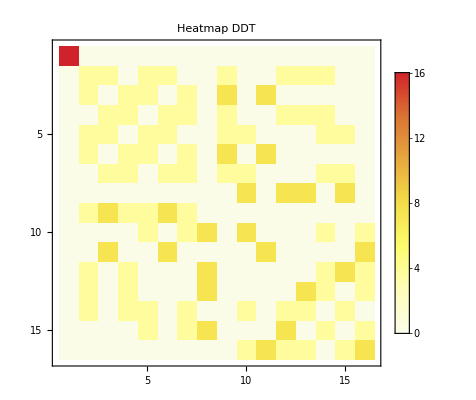

```mathematica
MatrixPlot[DDTMatrix,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameTicks->Automatic,PlotLabel->Style["Heatmap DDT",Bold,14]]
```

#### Probabilità di una transizione SBOX

```mathematica
(*PROBABILITA' DIFFERENZIALE DI UNA S-BOX*)
SBoxDiffProbability[dx_Integer,dy_Integer]:=DDTMatrix[[dx+1,dy+1]]/16;
```

```mathematica
Print["P(2 -> 1) = ",SBoxDiffProbability[2,1]];
```

P(2 -> 1) = 1/8

```mathematica
(*PROBABILITA' DEL SUBLAYER A 32 BIT*)
SubLayerDiffProbability[inputDiff_Integer,outputDiff_Integer]:=Module[{inNibbles,outNibbles,probabilities},
inNibbles=IntegerDigits[inputDiff,16,8];
outNibbles=IntegerDigits[outputDiff,16,8];
probabilities=MapThread[SBoxDiffProbability,{inNibbles,outNibbles}];
Times@@probabilities];
```

```mathematica
(*PROBABILITA' DI UNA TRANSIZIONE DI ROUND*)
RoundCharacteristicProbability[{dx0_,dx1_},{nextDx0_,nextDx1_}]:=Module[{sboxInput0,sboxInput1,sboxOutput0,sboxOutput1,p0,p1},
sboxInput0=dx0;
sboxInput1=BitXor[dx1,LeftRotate5[dx0]];
sboxOutput1=nextDx1;
sboxOutput0=BitXor[nextDx0,LeftRotate5[sboxOutput1]];
p0=SubLayerDiffProbability[sboxInput0,sboxOutput0];
p1=SubLayerDiffProbability[sboxInput1,sboxOutput1];
p0*p1];
```

```mathematica
(*CARATTERISTICA DIFFERENZIALE SINGLE-KEY (TABLE III)*)
characteristic={{16^^40000000,16^^0020A008},
{16^^00040000,16^^00802000},
{16^^00000000,16^^00004000},
{16^^00020000,16^^00001000},
{16^^10040000,16^^00801000},
{16^^50000100,16^^00002008},
{16^^40000000,16^^00000008},
{16^^40000000,16^^00000000},
{16^^10000040,16^^00000002},
{16^^40004010,16^^00000200}};
```

```mathematica
(*VERIFICA DELLA CARATTERISTICA DEL PAPER*)
roundProbabilities=Table[RoundCharacteristicProbability[characteristic[[r]],characteristic[[r+1]]],{r,1,9}];

Print["Probabilità delle nove transizioni:"];

TableForm[Table[{r,BaseForm[characteristic[[r]],16],BaseForm[characteristic[[r+1]],16],N[roundProbabilities[[r]]],Log[2,roundProbabilities[[r]]]},{r,1,9}],TableHeadings->{None,{"Round","Delta input","Delta output","Probabilità","log2(P)"}}]
```

Probabilità delle nove transizioni:

Round | Delta input | Delta output | Probabilità | log2(P)
1 | {40000000_16,(20a008)_16} | {40000_16,802000_16} | 0.0078125 | -7
2 | {40000_16,802000_16} | {0_16,4000_16} | 0.015625 | -6
3 | {0_16,4000_16} | {20000_16,1000_16} | 0.125 | -3
4 | {20000_16,1000_16} | {10040000_16,801000_16} | 0.00195313 | -9
5 | {10040000_16,801000_16} | {50000100_16,2008_16} | 0.000488281 | -11
6 | {50000100_16,2008_16} | {40000000_16,8_16} | 0.00390625 | -8
7 | {40000000_16,8_16} | {40000000_16,0_16} | 0.125 | -3
8 | {40000000_16,0_16} | {10000040_16,2_16} | 0.03125 | -5
9 | {10000040_16,2_16} | {40004010_16,200_16} | 0.00390625 | -8

```mathematica
totalProbability=Times@@roundProbabilities;

Print["Probabilità complessiva 9 round = ",N[totalProbability]];
Print["log2(P totale) = ",Log[2,totalProbability]];
```

Probabilità complessiva 9 round = 8.67362×10^-19

log2(P totale) = -60

```mathematica
(*PROBABILITA' CUMULATIVE*)
cumulativeProbabilities=FoldList[Times,1,roundProbabilities];

Print["Probabilità cumulative:"];
TableForm[Table[{r,N[cumulativeProbabilities[[r+1]]],Log[2,cumulativeProbabilities[[r+1]]]},{r,1,9}],TableHeadings->{None,{"Round completati","Probabilità cumulativa","log2(P)"}}]
```

Probabilità cumulative:

Round completati | Probabilità cumulativa | log2(P)
1 | 0.0078125 | -7
2 | 0.00012207 | -13
3 | 0.0000152588 | -16
4 | 2.98023×10^-8 | -25
5 | 1.45519×10^-11 | -36
6 | 5.68434×10^-14 | -44
7 | 7.10543×10^-15 | -47
8 | 2.22045×10^-16 | -52
9 | 8.67362×10^-19 | -60

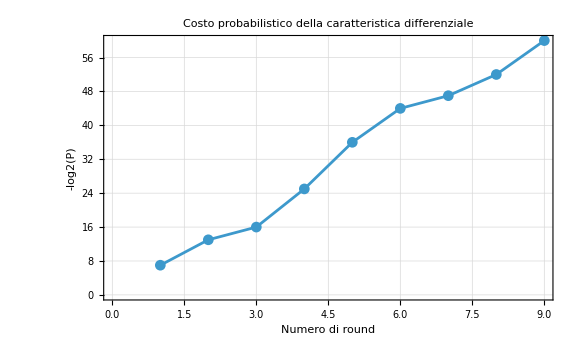

```mathematica
ListLinePlot[Table[{r,-Log[2,cumulativeProbabilities[[r+1]]]},{r,1,9}],PlotMarkers->Automatic,Frame->True,FrameLabel->{"Numero di round","-log2(P)"},PlotLabel->"Costo probabilistico della caratteristica differenziale",GridLines->Automatic,ImageSize->Large]
```

### VERIFICA EMPIRICA

```mathematica
(*cifratura che restituisce gli stati intermedi di ogni round,
per vedere se una coppia segue la specifica caratteristica differenziale del paper*)
LELBCEncryptTrace[plaintext_List,subkeys_List]:=Rest[FoldList[LELBCRound,plaintext,subkeys]];
```

```mathematica
(*VERIFICA EMPIRICA DI UN PREFISSO DELLA CARATTERISTICA*)
EmpiricalCharacteristicTest[rounds_Integer,nTests_Integer]:=Module[{masterKey,keys,matchesTrail=0,matchesOutput=0,P,Pprime,trace,tracePrime,differences,expectedDifferences},
masterKey=RandomInteger[{0,16^^FFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFF}];
keys=LELBCKeySchedule[masterKey,rounds];
(*differenze previste DOPO ciascun round*)
expectedDifferences=characteristic[[2;;rounds+1]];
Do[
P={RandomInteger[{0,16^^FFFFFFFF}],RandomInteger[{0,16^^FFFFFFFF}]};
Pprime={BitXor[P[[1]],characteristic[[1,1]]],BitXor[P[[2]],characteristic[[1,2]]]};
trace=LELBCEncryptTrace[P,keys];
tracePrime=LELBCEncryptTrace[Pprime,keys];
differences=MapThread[BitXor,{trace,tracePrime},2];
(*solo differenza finale*)
If[Last[differences]===Last[expectedDifferences],matchesOutput++];
(*intera caratteristica*)
If[differences===expectedDifferences,matchesTrail++];,{nTests}];
<|"Tests"->nTests,"Characteristic Matches"->matchesTrail,"Characteristic Empirical Probability"->N[matchesTrail/nTests],"Characteristic Theoretical Probability"->N[cumulativeProbabilities[[rounds+1]]],"Output Differential Matches"->matchesOutput,"Output Differential Probability"->N[matchesOutput/nTests]|>];
```

```mathematica
(*MONTE CARLO-3 ROUND*)
SeedRandom[12345];

result3=EmpiricalCharacteristicTest[3,1000000]
```

<|Tests→1000000,Characteristic Matches→14,Characteristic Empirical Probability→0.000014,Characteristic Theoretical Probability→0.0000152588,Output Differential Matches→34,Output Differential Probability→0.000034|>

```mathematica
(*COMPLESSITA' DEL MONTE CARLO*)requiredPairs=Table[{r,Log[2,1/(Times@@Take[roundProbabilities,r])]},{r,1,7}];

TableForm[requiredPairs,TableHeadings->{None,{"Round","log2(coppie per 1 right pair in media)"}}]
```

Round | log2(coppie per 1 right pair in media)
1 | 7
2 | 13
3 | 16
4 | 25
5 | 36
6 | 44
7 | 47

#### Riassunto propagazione della caratteristica

```mathematica
propagationTable=Table[{r,IntegerString[characteristic[[r,1]],16,8],IntegerString[characteristic[[r,2]],16,8],IntegerString[characteristic[[r+1,1]],16,8],IntegerString[characteristic[[r+1,2]],16,8],Log[2,roundProbabilities[[r]]],Log[2,Times@@Take[roundProbabilities,r]]},{r,1,7}];

TableForm[propagationTable,TableHeadings->{None,{"Round","Delta X0","Delta X1","Delta X0 successivo","Delta X1 successivo","log2(P round)","log2(P cumulativa)"}}]
```

Round | Delta X0 | Delta X1 | Delta X0 successivo | Delta X1 successivo | log2(P round) | log2(P cumulativa)
1 | 40000000 | 0020a008 | 00040000 | 00802000 | -7 | -7
2 | 00040000 | 00802000 | 00000000 | 00004000 | -6 | -13
3 | 00000000 | 00004000 | 00020000 | 00001000 | -3 | -16
4 | 00020000 | 00001000 | 10040000 | 00801000 | -9 | -25
5 | 10040000 | 00801000 | 50000100 | 00002008 | -11 | -36
6 | 50000100 | 00002008 | 40000000 | 00000008 | -8 | -44
7 | 40000000 | 00000008 | 40000000 | 00000000 | -3 | -47

## KEY RECOVERY

### Uso i primi 3 round come distinguisher e il round 4 come round di key recovery. In questo modo il distinguisher ha P=2^-16 e posso ottenere right pairs

input round 4:
ΔX0 = 00020000
ΔX1 = 00001000

prima di entrare nel sublayer: ΔX1 <- ΔX1 XOR (ΔX0 <<< 5) ovvero 00401000
dopo sublayer: ΔX1 <- ΔX1 XOR K1 ovvero 00801000

```mathematica
(*DIFFERENZA INTERNA DEL ROUND DI KEY RECOVERY*)
recoveryRound=4;
recoveryInputDiff=characteristic[[recoveryRound]];
(*Delta all'ingresso del sublayer destro del round 4*)
targetSBoxInput1=BitXor[recoveryInputDiff[[2]],LeftRotate5[recoveryInputDiff[[1]]]];

Print["ΔX1 ingresso S-box al 4 round ",recoveryRound,": ",IntegerString[targetSBoxInput1,16,8]];
```

ΔX1 ingresso S-box al 4 round 4: 00401000

```mathematica
(*CONTROLLO I NIBBLE DI K1 DA INDOVINARE*)
targetNibbles=IntegerDigits[targetSBoxInput1,16,8];

Print["Nibble della differenza: ",targetNibbles];
```

Nibble della differenza: {0,0,4,0,1,0,0,0}

```mathematica
(*GENERAZIONE DATI*)
SeedRandom[12345];

NtestsKR=2000000;
masterKeyKR=RandomInteger[{0,16^^FFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFF}];
keysKR=LELBCKeySchedule[masterKeyKR,recoveryRound];
realK1=keysKR[[recoveryRound,2]];

Print["K1 reale del round ",recoveryRound," = ",IntegerString[realK1,16,8]];
```

K1 reale del round 4 = fdabafb1

#### Filtraggio

```mathematica
(*RACCOLTA COPPIE CANDIDATE: 
seleziono direttamente i ciphertext che hanno una differenza compatibile con il round finale*)
inputDiffKR=characteristic[[1]];

expectedOutputAfterRecovery=characteristic[[recoveryRound+1]];
(*differenza prevista ramo destro dopo round*)
expectedRightBranchDiff=expectedOutputAfterRecovery[[2]];

activeOutputMask=Fold[BitOr,0,MapIndexed[If[#1!=0,BitShiftLeft[16^^F,4*(8-First[#2])],0]&,IntegerDigits[expectedRightBranchDiff,16,8]]];

Print["ΔX1 uscita S-box al 4 round ",recoveryRound,": ",IntegerString[expectedRightBranchDiff,16,8]]; 
Print["Maschera nibble attivi: ",IntegerString[activeOutputMask,16,8]];
```

ΔX1 uscita S-box al 4 round 4: 00801000

Maschera nibble attivi: 00f0f000

```mathematica
candidatePairs=Reap[Do[Module[{P,Pprime,C,Cprime,diffFirstCipherWord},P={RandomInteger[{0,16^^FFFFFFFF}],RandomInteger[{0,16^^FFFFFFFF}]};
Pprime={BitXor[P[[1]],inputDiffKR[[1]]],BitXor[P[[2]],inputDiffKR[[2]]]};
C=LELBCEncrypt[P,keysKR];
Cprime=LELBCEncrypt[Pprime,keysKR];
(*dopo lo swap finale C[[1]] è il ramo X1*)
diffFirstCipherWord=BitXor[C[[1]],Cprime[[1]]];
(*le differenze al di fuori dei nibble attivi devono essere zero*)
If[BitAnd[diffFirstCipherWord,BitXor[activeOutputMask,16^^FFFFFFFF]]==0,
Sow[{C,Cprime}]];],
{NtestsKR}]][[2]];

candidatePairs=If[candidatePairs==={},{},First[candidatePairs]];

Print["Coppie candidate dopo il filtro: ",Length[candidatePairs]];
```

Coppie candidate dopo il filtro: 121

```mathematica
(*POSIZIONI DEI NIBBLE DA RECUPERARE*)
activeInputPositions=Flatten[Position[Reverse[IntegerDigits[targetSBoxInput1,16,8]],x_/;x!=0]]-1;

Print["Posizioni nibble attivi = ",activeInputPositions];
```

Posizioni nibble attivi = {3,5}

```mathematica
(*2^8=256 GUESS*)
guessResults=Table[
Module[{nibbleA,nibbleB,partialKey,hits},
nibbleA=BitAnd[guess,16^^F];
nibbleB=BitAnd[BitShiftRight[guess,4],16^^F];
partialKey=BitOr[BitShiftLeft[nibbleA,4 activeInputPositions[[1]]],BitShiftLeft[nibbleB,4 activeInputPositions[[2]]]];
hits=Count[candidatePairs,pair_/;
Module[{u,uprime,du},
(*inversione dell'ultimo XOR con K1 e dell'sbox sui nibble interessati*)
u=ApplySubLayer[BitXor[pair[[1,1]],partialKey]];
uprime=ApplySubLayer[BitXor[pair[[2,1]],partialKey]];
du=BitXor[u,uprime];
(*controllo soltanto i nibble oggetto del guess*)
And@@Table[BitAnd[BitShiftRight[du,4 pos],16^^F]==BitAnd[BitShiftRight[targetSBoxInput1,4 pos],16^^F],{pos,activeInputPositions}]]];
{guess,partialKey,hits}],
{guess,0,255}];
```

#### Classifica key guess

```mathematica
sortedGuesses=Reverse[SortBy[guessResults,Last]];

top10=Take[sortedGuesses,Min[10,Length[sortedGuesses]]];

(*conversione in esadecimale per la visualizzazione*)
top10Formatted=Map[{IntegerString[#[[1]],16,2],IntegerString[#[[2]],16,8],#[[3]]}&,top10];

Print["Migliori 10 guess:"];

Print[TableForm[top10Formatted,TableHeadings->{None,{"Guess","Chiave parziale","Hits"}}]];
```

Migliori 10 guess:

Guess | Chiave parziale | Hits
aa | 00a0a000 | 62
8a | 0080a000 | 13
ae | 00a0e000 | 12
ab | 00a0b000 | 12
ba | 00b0a000 | 10
af | 00a0f000 | 9
3a | 0030a000 | 9
a1 | 00a01000 | 8
2a | 0020a000 | 8
a7 | 00a07000 | 7

```mathematica
(*CONFRONTO CON I NIBBLE REALI*)
realPartialKey=Fold[BitOr,0,Table[BitAnd[realK1,BitShiftLeft[16^^F,4 pos]],{pos,activeInputPositions}]];

bestPartialKey=sortedGuesses[[1,2]];

Print["Parte reale di K1 = ",IntegerString[realPartialKey,16,8]];

Print["Miglior guess = ",IntegerString[bestPartialKey,16,8]];

Print["Recovery corretto? ",bestPartialKey==realPartialKey];
```

Parte reale di K1 = 00a0a000

Miglior guess = 00a0a000

Recovery corretto? True

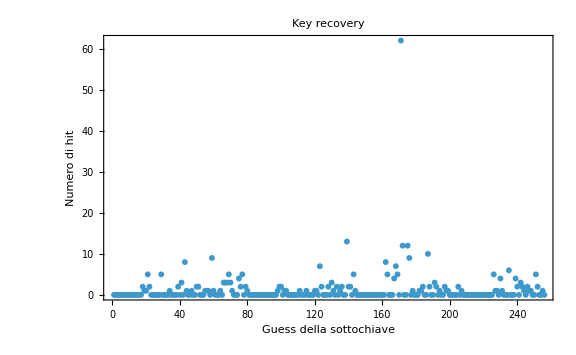

```mathematica
ListPlot[guessResults[[All,3]],PlotRange->All,Frame->True,FrameLabel->{"Guess della sottochiave","Numero di hit"},PlotLabel->"Key recovery",ImageSize->Large]
```